## Parameters

```mathematica
sampleSizeArray={50000,50000,50000,50000,50000,50000};
nArray={2,3,4,5,6,7};
alphaArray={2,2,2,2,2,2};
thetaArray={3,3,3,3,3,3};
(*colorArray=RandomColor[length];*)
(*colorArray={Orange,Red,Blue,Purple,Brown,Black};*)
colorArray={Red,Blue,Black,Red,Blue,Brown,Black};
rootDir="D:\\research\\eigenvectors\\simulations\\data\\finite";

simulatedDataFile="simulation_1.mx";
analyticalDataFile="analytical_min_1.mx";


If[
Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}]<Max[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}],Print["Missing parameters!!"];length=0;,
length=Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}];
];
simulatedDataFile=FileNameJoin[{rootDir,simulatedDataFile}];
analyticalDataFile=FileNameJoin[{rootDir,analyticalDataFile}];
```

## Samples generation

```mathematica
Print["Time taken to generate samples: ",AbsoluteTiming[simDataArray=Table[
n=nArray[[t]];
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
sampleSize=sampleSizeArray[[t]];

m=n+alpha;
u=Table[x,{x,Normalize[RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],n].{1.,0}]}];
sigma = FullSimplify[IdentityMatrix[n]+theta*Outer[Times,u,Conjugate[u]]];

ParallelTable[
A=Table[Flatten[RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]+I*RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]],m];
W=ConjugateTranspose[A].A; 
eigSys=Eigensystem[W];
{eigSys[[1]],eigSys[[2]],u}
,sampleSize],
{t,1,length}];][[1]]," seconds"];
AppendTo[simDataArray,{sampleSizeArray,nArray,alphaArray,thetaArray}];
Print["Exported to: ",Export[simulatedDataFile,simDataArray]];
```

Time taken to generate samples: 350.617 seconds

Exported to: D:\research\eigenvectors\simulations\data\finite\simulation_7.mx

## Analytical expression

```mathematica
Clear[pdf];

(********************************** min eigenvector ****************************)

(*generic pdf min eigvec for zero alpha*)
(*
anaMin=0; anaMax=1;dz=0.005;
description="generic pdf min eigvec for zero alpha"; 
pdf[z_,n_,alpha_,theta_,beta_]:=(n*(n-1))/((theta+1)^n*(n-theta/(theta+1)))*(1-z)^(n-2)/(1-theta/(theta+1)(1-z))^(n+1);
*)


(*generic pdf min eigvec for n>=2*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="generic pdf min eigvec for n>=2"; 
A[n_,alpha_]:=((n+alpha)!)/(theta+1)^(n+alpha);
pdf[z_,n_,alpha_,theta_,beta_]:=If[theta>0,If[n>2,A[n,alpha]*Sum[
B=Flatten[ParallelTable[
kjs={k1,k2,k3,k4,k5, k6, k7, k8, k9, k10};
sumk=Total[kjs];

mat=Flatten[{{Table[If[k==i1,1/((n+i1-1)!),0],{i1,1,alpha+1}] },Table[1/((n+i-j-kjs[[j-1]]-1)!),{j,2,alpha+1},{i,1,alpha+1}]},1];
(*Print[k," ",k1," ",k2," ",MatrixForm[mat]];*)
   (∏_(j=1)^alpha (((n+alpha-j-1)!)/((j+1+kjs[[j]])!*(kjs[[j]])!)))*((alpha+sumk)!)/(n-theta/(theta+1))^(alpha+sumk+1)*Det[mat]

,{k1,0,If[n+alpha-2>n-2,n+alpha-2,0]},{k2,0,If[n+alpha-3>n-2,n+alpha-3,0]},{k3,0,If[n+alpha-4>n-2,n+alpha-4,0]},{k4,0,If[n+alpha-5>n-2,n+alpha-5,0]},{k5,0,If[n+alpha-6>n-2,n+alpha-6,0]},{k6,0,If[n+alpha-7>n-2,n+alpha-7,0]},{k7,0,If[n+alpha-8>n-2,n+alpha-8,0]},{k8,0,If[n+alpha-9>n-2,n+alpha-9,0]},{k9,0,If[n+alpha-10>n-2,n+alpha-10,0]},{k10,0,If[n+alpha-11>n-2,n+alpha-11,0]}]];
((n+k-1)*(n+k-2)*(-theta/(theta+1))^(k-1)*(1-z)^(n+k-3))/(1-theta/(theta+1)*(1-z))^(n+k)*Sum[B[[h]],{h,1,Length[B]}],{k,1,alpha+1}],
(1-beta)^(2+alpha)/((alpha+1)!)Sum[(((k+2)!*(2*alpha-k)!)/(k!(alpha-k)!*(2-beta)^(2*alpha-k+1)*(1-beta*(1-z))^(k+3))),{k,0,alpha}]],
(n-1)*(1-z)^(n-2)];
*)



(*generic pdf min eigvec for n=2*)
(*
anaMin=0; anaMax=1;dz=0.005;
description=generic pdf min eigvec for n=2;
pdf[z_,n_,alpha_,theta_,beta_]:=(1-beta)^(2+alpha)/((alpha+1)!)Sum[(((k+2)!*(2*alpha-k)!)/(k!(alpha-k)!*(2-beta)^(2*alpha-k+1)*(1-beta*(1-z))^(k+3))),{k,0,alpha}];
*)





(********************************** max eigenvector ****************************)

(*generic pdf max eigvec for n=2 simplified*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="generic pdf max eigvec for n=2 simplified"; 
pdf[z_,n_,alpha_,theta_,beta_]:=1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*(Beta[3,alpha+1]*(2*alpha+3)!)/((theta+1)^(2+alpha)*(2-beta)^(2*alpha+4))*Hypergeometric2F1[3,2*alpha+4,alpha+4,(1-beta(1-z))/(2-beta)];
*)



(*max eigvec n<=3, any alpha*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="max eigvec n<=3, any alpha"; 

delta[z_,beta_]:=(1-beta*(1-z))/(1-beta*z);
pdf[z_,n_,alpha_,theta_,beta_]:=If[n==3,
If[theta>0,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*2/((theta+1)^(n+alpha)*beta)*(3*alpha+7)!*(Beta[alpha+1,3]*Beta[alpha+2,3])/((1-beta*z)^(2*alpha+6)*(2-beta*z)^(alpha+1))*(Sum[(Pochhammer[-2*alpha-4,k]*Pochhammer[alpha+1,k])/(Pochhammer[alpha+4,k]*k!*(1-beta*z)*(2-beta*z)^k)*AppellF1[alpha+2,2*alpha+7,alpha+k+1,alpha+5,(beta*(1-z)-1)/(1-beta*z),(beta*(1-z)-1)/(2-beta*z)],{k,0,2*alpha+4}]-Sum[(Pochhammer[-2*alpha-3,k]*Pochhammer[alpha+2,k])/(Pochhammer[alpha+5,k]*k!*(2-beta*z)^(k+1))*AppellF1[alpha+1,2*alpha+6,alpha+k+2,alpha+4,(beta*(1-z)-1)/(1-beta*z),(beta*(1-z)-1)/(2-beta*z)],{k,0,2*alpha+3}]),(n-1)*(1-z)^(n-2)],

((2*alpha+3)!)/((alpha+1)!*alpha!*(theta+1)^(n+alpha))*1/(1-beta*z)^(2*alpha+4)*(Hypergeometric2F1[2*alpha+4,alpha+1,2+alpha,-delta[z,beta]]/(alpha+1)-2*Hypergeometric2F1[2*alpha+4,alpha+2,alpha+3,-delta[z,beta]]/(alpha+2)+Hypergeometric2F1[2*alpha+4,alpha+3,alpha+4,-delta[z,beta]]/(alpha+3))

]
*)



(*max eigvec n<=3, any alpha, simplified version*)
(*
anaMin=0; anaMax=1;dz=0.01;
description="max eigvec n<=3, any alpha, simplified version"; 
delta[z_,beta_]:=(1-beta*(1-z))/(3-beta);
appellF2[a_,b1_,b2_,c1_,c2_,x_,y_]:=Sum[(Pochhammer[a,m+n]*Pochhammer[b1,m]*Pochhammer[b2,n])/(Pochhammer[c1,m]*Pochhammer[c2,n]*m!*n!)*x^m*y^n,{m,0,50},{n,0,50}];
pdf[z_,n_,alpha_,theta_,beta_]:=If[n==3,
If[theta>0,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*2/((theta+1)^(n+alpha)*beta)*(3*alpha+7)!*(Beta[alpha+1,3]*Beta[alpha+2,3])/((3-beta)^(n^2+n*alpha-n+2))*(appellF2[n^2+n*alpha-n+2,3,3,alpha+4,alpha+5,1/(3-beta),delta[z,beta]]-appellF2[n^2+n*alpha-n+2,3,3,alpha+5,alpha+4,1/(3-beta),delta[z,beta]]),(n-1)*(1-z)^(n-2)],

((2*alpha+3)!)/((alpha+1)!*alpha!*(theta+1)^(n+alpha))*1/(1-beta*z)^(2*alpha+4)*(1/(alpha+1)Hypergeometric2F1[2*alpha+4,alpha+1,2+alpha,-delta[z,beta]]-2*1/(alpha+2)Hypergeometric2F1[2*alpha+4,alpha+2,alpha+3,-delta[z,beta]]+1/(alpha+3)Hypergeometric2F1[2*alpha+4,alpha+3,alpha+4,-delta[z,beta]])

]
*)


(*generic pdf max eigvec for n=4*)
(*
anaMin=0; anaMax=1;dz=0.1;
description="generic pdf max eigvec for n=4"; 
appellFA[a_,b1_,b2_,b3_,c1_,c2_,c3_,u_,v_,w_]:=Sum[((Pochhammer[a,p+q+r]*Pochhammer[b1,p]*Pochhammer[b2,q]*Pochhammer[b3,r])/(Pochhammer[c1,p]*Pochhammer[c2,q]*Pochhammer[c3,r]*p!*q!*r!))*u^p*v^q*w^r,{p,0,10},{q,0,10},{r,0,10}];
appellFAMod[n_,alpha_,c1_,c2_,c3_,beta_,z_]:=appellFA[n^2+n*alpha-n+2,3,3,3,c1,c2,c3,1/(4-beta),1/(4-beta),(1-beta(1-z))/(4-beta)];
pdf[z_,n_,alpha_,theta_,beta_]:=1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*((n-1)*(n^2+n*alpha-n+1)!)/((theta+1)^(n+alpha)*beta^(n-2)*(4-beta)^(n^2+n*alpha-n+2))*(Beta[3,alpha+1]*(Beta[3,alpha+3])^2*appellFAMod[n,alpha,alpha+4,alpha+6,alpha+6,beta,z]-Beta[3,alpha+1]*(Beta[3,alpha+3])^2*appellFAMod[n,alpha,alpha+6,alpha+6,alpha+4,beta,z]+Beta[2,alpha+1]*Beta[2,alpha+2]*Beta[3,alpha+4]*appellFAMod[n,alpha,alpha+5,alpha+7,alpha+4,beta,z]-Beta[3,alpha+1]*Beta[3,alpha+2]*Beta[3,alpha+4]*appellFAMod[n,alpha,alpha+4,alpha+7,alpha+5,beta,z]+Beta[3,alpha+3]*(Beta[3,alpha+2])^2*appellFAMod[n,alpha,alpha+5,alpha+6,alpha+5,beta,z]-Beta[3,alpha+3]*(Beta[3,alpha+2])^2*appellFAMod[n,alpha,alpha+5,alpha+5,alpha+6,beta,z]);
*)


(*generic pdf max eigvec for n=4 with F2*)
(*
anaMin=0.0; anaMax=0.9;dz=0.1;
description="generic pdf max eigvec for n=4 with F2 explicit"; 
(*appellF2[a_,b1_,b2_,c1_,c2_,x_,y_]:=Sum[(Pochhammer[a,p+q]*Pochhammer[b1,p]*Pochhammer[b2,q])/(Pochhammer[c1,p]*Pochhammer[c2,q]*p!*q!)*x^p*y^q,{p,0,100},{q,0,100}];*)
appellF2[phi_,beta_,gamma_,w_]:=(Gamma[beta]*Gamma[gamma])/(Gamma[3]*Gamma[3]*Gamma[beta-3]*Gamma[gamma-3])*NIntegrate[u^2*v^2*(1-u)^(beta-4)*(1-v)^(gamma-4)*(1-u*w-v*w)^-phi,{u,0,1},{v,0,1}];
(*i1[w_,mu_,phi_,a_,b_]:=1/w^3*Sum[Binomial[b,j]*Binomial[a,k]*Binomial[j+k+2,l]*(-1)^(j+k+l)/w^k*mu^(j+k+2-l)/(phi-l-1)*(1/(mu-w)^(phi-l-1)-1/mu^(phi-l-1)),{j,0,b},{k,0,a},{l,0,j+k+2}];
appellF2[phi_,beta_,gamma_,w_]:=(Gamma[beta]*Gamma[gamma])/(Gamma[3]*Gamma[3]*Gamma[beta-3]*Gamma[gamma-3])*1/w^3*Sum[Binomial[beta-4,k]*Binomial[k+2,l]*(-1)^(k+l)/(w^k*(phi-l-1))*(i1[w,1-w,phi-l-1,gamma-4,k+2-l]-i1[w,1,phi-l-1,gamma-4,k+2-l]),{k,0,beta-4},{l,0,k+2}];*)

g[NN_,b_,c_,alpha_,beta_,z_]:=1/(∏_(i=1)^4 ((4+alpha-i)!*(4-i)!))*6/((beta/(1-beta)+1)^(4+alpha)*beta^2)*Beta[3,b+alpha-3]*Beta[3,c+alpha-3]*((NN+alpha)!)/(1-beta*(1-z))^(NN+alpha+1)*(((12+3*alpha-NN)!)/(3-beta*z)^(13+3*alpha-NN)*appellF2[13+3*alpha-NN,b+alpha,c+alpha,1/(3-beta*z)]-Sum[((12+3*alpha+k-NN)!*(1-beta*(1-z))^k)/(k!*(4-beta)^(13+3*alpha-NN+k))*appellF2[13+3*alpha-NN+k,b+alpha,c+alpha,1/(4-beta)],{k,0,NN+alpha}]);
pdf[z_,n_,alpha_,theta_,beta_]:=(g[2,4,6,alpha,beta,z]-g[2,5,5,alpha,beta,z]-2*g[3,4,6,alpha,beta,z]+2*g[3,5,5,alpha,beta,z]+g[4,4,6,alpha,beta,z]-g[4,5,5,alpha,beta,z]+g[1,5,6,alpha,beta,z]-g[1,4,7,alpha,beta,z]-2*g[2,5,6,alpha,beta,z]+2*g[2,4,7,alpha,beta,z]+g[3,5,6,alpha,beta,z]-g[3,4,7,alpha,beta,z]+g[0,5,7,alpha,beta,z]-g[0,6,6,alpha,beta,z]-2*g[1,5,7,alpha,beta,z]+2*g[1,6,6,alpha,beta,z]+g[2,5,7,alpha,beta,z]-g[2,6,6,alpha,beta,z]);
*)


(*generic pdf max eigvec for n<=4*)
(*
anaMin=0; anaMax=1;dzArray={0.005,0.005,0.005,0.0005,0.0005,0.0005,0.0005};
description="max eigvec n<=4, any alpha";
delta[n_,z_,beta_]:=(1-beta*(1-z))/(n-beta);
appellF2[a_,b1_,b2_,c1_,c2_,x_,y_]:=Sum[(Pochhammer[a,m+n]*Pochhammer[b1,m]*Pochhammer[b2,n])/(Pochhammer[c1,m]*Pochhammer[c2,n]*m!*n!)*x^m*y^n,{m,0,160},{n,0,160}];
appellF2Int[phi_,beta_,gamma_,w_]:=(Gamma[beta]*Gamma[gamma])/(Gamma[3]*Gamma[3]*Gamma[beta-3]*Gamma[gamma-3])*NIntegrate[u^2*v^2*(1-u)^(beta-4)*(1-v)^(gamma-4)*(1-u*w-v*w)^-phi,{u,0,1},{v,0,1}];
g[NN_,b_,c_,alpha_,beta_,z_]:=1/(∏_(i=1)^4 ((4+alpha-i)!*(4-i)!))*6/((beta/(1-beta)+1)^(4+alpha)*beta^2)*Beta[3,b+alpha-3]*Beta[3,c+alpha-3]*((NN+alpha)!)/(1-beta*(1-z))^(NN+alpha+1)*(((12+3*alpha-NN)!)/(3-beta*z)^(13+3*alpha-NN)*appellF2Int[13+3*alpha-NN,b+alpha,c+alpha,1/(3-beta*z)]-Sum[((12+3*alpha+k-NN)!*(1-beta*(1-z))^k)/(k!*(4-beta)^(13+3*alpha-NN+k))*appellF2Int[13+3*alpha-NN+k,b+alpha,c+alpha,1/(4-beta)],{k,0,NN+alpha}]);
pdf[z_,n_,alpha_,theta_,beta_]:=Switch[n,
2,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*(Beta[3,alpha+1]*(2*alpha+3)!)/((theta+1)^(n+alpha)*(2-beta)^(2*alpha+4))*Hypergeometric2F1[3,2*alpha+4,alpha+4,delta[n,z,beta]],

3,If[theta>0,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*2/((theta+1)^(n+alpha)*beta)*(3*alpha+7)!*(Beta[alpha+1,3]*Beta[alpha+2,3])/((3-beta)^(n^2+n*alpha-n+2))*(appellF2[n^2+n*alpha-n+2,3,3,alpha+4,alpha+5,1/(3-beta),delta[n,z,beta]]-appellF2[n^2+n*alpha-n+2,3,3,alpha+5,alpha+4,1/(3-beta),delta[n,z,beta]]),(n-1)*(1-z)^(n-2)],

4,g[2,4,6,alpha,beta,z]-g[2,5,5,alpha,beta,z]-2*g[3,4,6,alpha,beta,z]+2*g[3,5,5,alpha,beta,z]+g[4,4,6,alpha,beta,z]-g[4,5,5,alpha,beta,z]+g[1,5,6,alpha,beta,z]-g[1,4,7,alpha,beta,z]-2*g[2,5,6,alpha,beta,z]+2*g[2,4,7,alpha,beta,z]+g[3,5,6,alpha,beta,z]-g[3,4,7,alpha,beta,z]+g[0,5,7,alpha,beta,z]-g[0,6,6,alpha,beta,z]-2*g[1,5,7,alpha,beta,z]+2*g[1,6,6,alpha,beta,z]+g[2,5,7,alpha,beta,z]-g[2,6,6,alpha,beta,z]
] ;
*)


(*generic pdf max eigvec for n=5*)
(*
anaMin=0; anaMax=1;dzArray={0.05,0.05,0.05};
description="max eigvec n=5, any alpha"; 
ff[alpha_,j_,i_,x_]:=Beta[3,i+j+alpha-1]*Hypergeometric1F1[alpha+i+j-1,alpha+i+j+2,-x];
g[z_,n_,alpha_,theta_,beta_,x_]:=NIntegrate[Exp[-(1-(1-z)*beta)*x*t]*t^alpha*(1-t)^2*Det[Table[t*ff[alpha,j,i,x]-ff[alpha+1,j,i,x],{j,1,n-2},{i,1,n-2}]],{t,0,1}];
pdf[z_,n_,alpha_,theta_,beta_]:=((n-1)!*(1-beta)^(n+alpha))/beta^(n-2)*1/Product[(n-j)!*(n+alpha-j)!,{j,1,n}]*NIntegrate[x^(n^2+n*alpha-n+1)*Exp[-(1-beta*z)*x]*g[z,n,alpha,theta,beta,x],{x,0,Infinity}];
*)


(*generic pdf max eigvec for n≤5*)
anaMin=0; anaMax=1;dzArray={0.005,0.005,0.005,0.005,0.005,0.005};
description="max eigvec n<=5, any alpha";
delta[n_,z_,beta_]:=(1-beta*(1-z))/(n-beta);
appellF2[a_,b1_,b2_,c1_,c2_,x_,y_]:=Sum[(Pochhammer[a,m+n]*Pochhammer[b1,m]*Pochhammer[b2,n])/(Pochhammer[c1,m]*Pochhammer[c2,n]*m!*n!)*x^m*y^n,{m,0,160},{n,0,160}];
appellF2Int[phi_,beta_,gamma_,w_]:=(Gamma[beta]*Gamma[gamma])/(Gamma[3]*Gamma[3]*Gamma[beta-3]*Gamma[gamma-3])*NIntegrate[u^2*v^2*(1-u)^(beta-4)*(1-v)^(gamma-4)*(1-u*w-v*w)^-phi,{u,0,1},{v,0,1}];
g[NN_,b_,c_,alpha_,beta_,z_]:=1/(∏_(i=1)^4 ((4+alpha-i)!*(4-i)!))*6/((beta/(1-beta)+1)^(4+alpha)*beta^2)*Beta[3,b+alpha-3]*Beta[3,c+alpha-3]*((NN+alpha)!)/(1-beta*(1-z))^(NN+alpha+1)*(((12+3*alpha-NN)!)/(3-beta*z)^(13+3*alpha-NN)*appellF2Int[13+3*alpha-NN,b+alpha,c+alpha,1/(3-beta*z)]-Sum[((12+3*alpha+k-NN)!*(1-beta*(1-z))^k)/(k!*(4-beta)^(13+3*alpha-NN+k))*appellF2Int[13+3*alpha-NN+k,b+alpha,c+alpha,1/(4-beta)],{k,0,NN+alpha}]);
ff[alpha_,j_,i_,x_]:=Beta[3,i+j+alpha-1]*Hypergeometric1F1[alpha+i+j-1,alpha+i+j+2,-x];
gg[z_,n_,alpha_,theta_,beta_,x_]:=NIntegrate[Exp[-(1-(1-z)*beta)*x*t]*t^alpha*(1-t)^2*Det[Table[t*ff[alpha,j,i,x]-ff[alpha+1,j,i,x],{j,1,n-2},{i,1,n-2}]],{t,0,1}];
pdf[z_,n_,alpha_,theta_,beta_]:=Switch[n,
2,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*(Beta[3,alpha+1]*(2*alpha+3)!)/((theta+1)^(n+alpha)*(2-beta)^(2*alpha+4))*Hypergeometric2F1[3,2*alpha+4,alpha+4,delta[n,z,beta]],

3,If[theta>0,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*2/((theta+1)^(n+alpha)*beta)*(3*alpha+7)!*(Beta[alpha+1,3]*Beta[alpha+2,3])/((3-beta)^(n^2+n*alpha-n+2))*(appellF2[n^2+n*alpha-n+2,3,3,alpha+4,alpha+5,1/(3-beta),delta[n,z,beta]]-appellF2[n^2+n*alpha-n+2,3,3,alpha+5,alpha+4,1/(3-beta),delta[n,z,beta]]),(n-1)*(1-z)^(n-2)],

4,g[2,4,6,alpha,beta,z]-g[2,5,5,alpha,beta,z]-2*g[3,4,6,alpha,beta,z]+2*g[3,5,5,alpha,beta,z]+g[4,4,6,alpha,beta,z]-g[4,5,5,alpha,beta,z]+g[1,5,6,alpha,beta,z]-g[1,4,7,alpha,beta,z]-2*g[2,5,6,alpha,beta,z]+2*g[2,4,7,alpha,beta,z]+g[3,5,6,alpha,beta,z]-g[3,4,7,alpha,beta,z]+g[0,5,7,alpha,beta,z]-g[0,6,6,alpha,beta,z]-2*g[1,5,7,alpha,beta,z]+2*g[1,6,6,alpha,beta,z]+g[2,5,7,alpha,beta,z]-g[2,6,6,alpha,beta,z],


_?(#>4&),((n-1)!*(1-beta)^(n+alpha))/beta^(n-2)*1/Product[(n-j)!*(n+alpha-j)!,{j,1,n}]*NIntegrate[x^(n^2+n*alpha-n+1)*Exp[-(1-beta*z)*x]*gg[z,n,alpha,theta,beta,x],{x,0,Infinity}]
] ;









If[Length[dzArray]==length,
Print["Time taken to generate curves: ",AbsoluteTiming[anaDataArray=ParallelTable[
n=nArray[[t]];
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
m=n+alpha;
beta=theta/(theta+1);
{z,pdf[z,n,alpha,theta,beta]},{t,1,length},{z,anaMin,anaMax,dzArray[[t]]}];]];
AppendTo[anaDataArray,{description,nArray,alphaArray,thetaArray}];
Print["Exported to: ",Export[analyticalDataFile,anaDataArray]],

Print["dz length mismatch!"]];
```

NIntegrate::inumr: The integrand (2 «3» (((Notebook$$25$645022`t («9»+Plus[«9»] Plus[«2»]))/1814400+(9 Power[«2»] Plus[«9»] Power[«2»]+«17»)/19958400) («1»)-((«21» «1»)/181440+(«1»)/(«7»)) («1»)+«1»-((Notebook$$25$645022`t («1»))/2520+(«1»)/20160) («1»)))/(Notebook$$25$645022`x)^9 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-0.25 Notebook$$25$645022`t Notebook$$25$645022`x) (1-Notebook$$25$645022`t)^2 (Notebook$$25$645022`t)^2 («6»+((Notebook$$25$645022`t («1»))/20160+(7 Power[«2»] Plus[«7»] Power[«2»]+«13»)/181440) («1»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (2 «3» (((Notebook$$25$645022`t («9»+Plus[«9»] Plus[«2»]))/1814400+(9 Power[«2»] Plus[«9»] Power[«2»]+«17»)/19958400) («1»)-((«21» «1»)/181440+(«1»)/(«7»)) («1»)+«1»-((Notebook$$25$645022`t («1»))/2520+(«1»)/20160) («1»)))/(Notebook$$25$645022`x)^9 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-1. Notebook$$25$645022`x) (Notebook$$25$645022`x)^43 NIntegrate[Exp[-(1+Times[«2»]) Notebook$$25$645022`x Notebook$$25$645022`t] (Notebook$$25$645022`t)^2 (1-Notebook$$25$645022`t)^2 Det[Table[Notebook$$25$645022`t Notebook$$25$645022`ff[«4»]-Notebook$$25$645022`ff[«4»],{Notebook$$25$645022`j,1,6-2},{Notebook$$25$645022`i,1,6-2}]],{Notebook$$25$645022`t,0,1}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-1. Notebook$$25$645022`x) (Notebook$$25$645022`x)^57 NIntegrate[Exp[-(1+Times[«2»]) Notebook$$25$645022`x Notebook$$25$645022`t] (Notebook$$25$645022`t)^2 (1-Notebook$$25$645022`t)^2 Det[Table[Notebook$$25$645022`t Notebook$$25$645022`ff[«4»]-Notebook$$25$645022`ff[«4»],{Notebook$$25$645022`j,1,7-2},{Notebook$$25$645022`i,1,7-2}]],{Notebook$$25$645022`t,0,1}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-0.25 Notebook$$25$645022`t Notebook$$25$645022`x) (1-Notebook$$25$645022`t)^2 (Notebook$$25$645022`t)^2 («6»+((Notebook$$25$645022`t («1»))/20160+(7 Power[«2»] Plus[«7»] Power[«2»]+«13»)/181440) («1»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (8 ⅇ^(«1») «1»«1»«1» (-(Notebook$$25$645022`x)^2 (-2520+«20»+«1»-(«21»)^5+Notebook$$25$645022`t («21»)^5) (907200 Notebook$$25$645022`x-1814400 ⅇ^(Notebook$$25$645022`x) Notebook$$25$645022`x+«70»+«14»)+«1»+(«1») («1»)))/(Notebook$$25$645022`x)^27 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {48.7099}. NIntegrate obtained -256.028 and 470.663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {42.5792}. NIntegrate obtained 1.88922×10^16 and 5.32227×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {48.7522}. NIntegrate obtained 4.49819×10^15 and 2.95715×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {68.1055}. NIntegrate obtained 3.39874×10^14 and 3.72189×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {42.6662}. NIntegrate obtained 2.82688×10^25 and 8.39353×10^20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {42.6662}. NIntegrate obtained 2.62808×10^25 and 9.57045×10^20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$25$645022`x near {Notebook$$25$645022`x} = {42.6662}. NIntegrate obtained 2.41776×10^25 and 1.19294×10^21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Time taken to generate curves: {12757.1,Null}

Exported to: D:\research\eigenvectors\simulations\data\finite\analytical_max_7.mx

## Import data

```mathematica
simDataArray=Import[simulatedDataFile];
anaDataArray=Import[analyticalDataFile];
simulationInfo=Last[simDataArray];
Print["Simulation parameters: \nsample size="<>ToString[simulationInfo[[1]]]<>"\nn="<>ToString[simulationInfo[[2]]]<>"\nα="<>ToString[simulationInfo[[3]]]<>"\nθ="<>ToString[simulationInfo[[4]]]];
analyticalInfo=Last[anaDataArray];
Print["Analytical expression paranmeters:\nDescription:"<>ToString[analyticalInfo[[1]]]<>"\nn="<>ToString[analyticalInfo[[2]]]<>"\nα="<>ToString[analyticalInfo[[3]]]<>"\nθ="<>ToString[analyticalInfo[[4]]]];
If[analyticalInfo[[2;;]]≠simulationInfo[[2;;]],Print["Warning! Different parameter sets!!"]];
nArray=analyticalInfo[[2]];
alphaArray=analyticalInfo[[3]];
thetaArray=analyticalInfo[[4]];
length=Length[nArray];
```

Simulation parameters: 
sample size={5000, 5000, 5000, 5000, 5000, 5000, 5000}
n={2, 5, 10, 3, 3, 3, 3}
α={2, 2, 2, 2, 2, 2, 2}
θ={3, 3, 3, 0, 5, 10, 20}

Analytical expression paranmeters:
Description:generic pdf min eigvec for n>=2
n={2, 5, 10, 3, 3, 3, 3}
α={2, 2, 2, 2, 2, 2, 2}
θ={3, 3, 3, 0, 5, 10, 20}

## Histogram

```mathematica
binsArray={{0.03,0.03,0.03,0.01,0.01,0.01,0.01},False}; (*True->use as no. of bins, False->use as dx*)

simVectorArray=Table[
simData=simDataArray[[t]];
simVector=Table[
eigVals=simData[[i,1]];
eigVecs=simData[[i,2]];
u=simData[[i,3]];

(*squared absolute value of minimum eigenvector inner product with u*)
(Abs[Last[eigVecs].u])^2

(*squared absolute value of maximum eigenvector inner product with u*)
(*(Abs[First[eigVecs].u])^2*)

,{i,1,Length[simData]}]
,{t,1,length}];

histArray=Table[
simVector=simVectorArray[[t]];
hist=Histogram[simVector,Automatic,PDF,ImageSize->Medium,ChartStyle->colorArray[[t]]],
{t,1,length}];

simDistArray=Table[
hist=histArray[[t]];
bins=binsArray[[1,t]];
useBins=binsArray[[2]];
simVector=simVectorArray[[t]];

min=First[PlotRange/.Options[hist,PlotRange]][[1]];
max=First[PlotRange/.Options[hist,PlotRange]][[2]];
dx=If[useBins,(max-min)/bins,bins];
simDist=HistogramDistribution[simVector,{dx}];
{min,max,dx,simDist},
{t,1,length}];
```

## Plotting

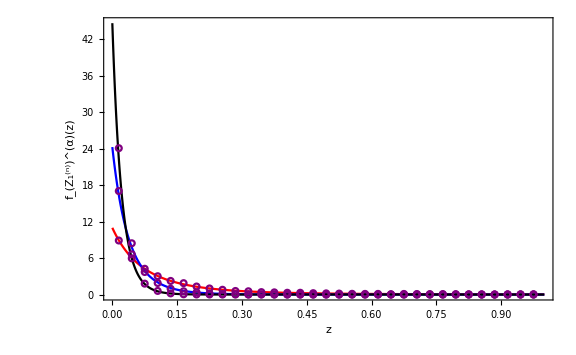

```mathematica
gStart=1; gEnd=3;
newMin=0; newMax=1;
legendCoord={0.75,0.75};

stringArray = Table[
"n="<>ToString [nArray[[t]]]
(*"θ="<>ToString [thetaArray[[t]]]*)
(*"n="<>ToString [nArray[[t]]]<>", θ="<>ToString [thetaArray[[t]]]<>", α="<>ToString[alphaArray[[t]]]*)
,{t,gStart,gEnd}];



gStart=Max[gStart,1]; gEnd=Min[gEnd,length];
legendPlotted=False;
oldMin=simDistArray[[All,1]]; oldMax=simDistArray[[All,2]];
newMin=Table[newMin,length];
newMax=Table[newMax,length];

plotArray=Table[
min=newMin[[t]];
max=newMax[[t]];
dx=simDistArray[[t,3]];
simDist=simDistArray[[t,4]];
hist=histArray[[t]];
color=colorArray[[t]];

thePlot=If[legendPlotted,
(*ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color],*)
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color],
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color,PlotLegends->Placed[LineLegend[colorArray[[gStart;;gEnd]],stringArray],legendCoord]]];

simDataPoints=Table[{x+dx/2,PDF[simDist,x+dx/2]},{x,min,max-dx/2,dx}];
simPlot=If[legendPlotted,
ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6]],
legendPlotted=True;ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6],PlotLegends->Placed[{"Simulation"},legendCoord]]];

{thePlot,simPlot,hist,color},
{t,gStart,gEnd}];

Show[Flatten[{plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},PlotRangePadding->{{0},{0.0}},ImageSize->Large, Frame->True,FrameLabel->{{"f_(Z_1^(n))^(α)(z)",None},{"z",None}}, FrameStyle->Directive[Automatic, 15, Bold]]
(*Frame labels
	FrameLabel->{{ToExpression["f_{Z_{N}}^\\alpha(z)", TeXForm],None},{"z",None}}
*)
(*Show[Flatten[{histArray[[All]],plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},ImageSize->Large]*)
```